# IPPT Model

## 2. Single Case Solver

Instructions:
- This notebook will evaluate the model using a single set of input conditions

How to Run:
- Define the input conditions you desire
- Click “Evaluate Notebook in Menu Options”
- Only the time-to-solution will be output explicitly, use “3. Single Case Plots” to visualize model results

## Inputs

Notes:
- Inputs loaded from csv file with name “DataIO-Run#.csv”
- Evaluate first cell then click “Browse...” button below to find csv file

```mathematica
Clear[DataIOFile]
FileNameSetter[Dynamic[DataIOFile],"OpenList"]
```

$CellContext`DataIOFileOpenListAll

```mathematica
(** Evaluate this to load csv file data **)
MasterTable=Import[DataIOFile[[1]]];
Nsols=Dimensions[MasterTable][[1]]-1

(** Generate Tables of Data from MasterTable **)

zmaxT=MasterTable[[2;;Nsols+1,1]];
zstepsT=MasterTable[[2;;Nsols+1,2]];
tmaxT=MasterTable[[2;;Nsols+1,3]];
tstepsT=MasterTable[[2;;Nsols+1,4]];
zs0T=MasterTable[[2;;Nsols+1,5]];
ws0T=MasterTable[[2;;Nsols+1,6]];
nn0T=MasterTable[[2;;Nsols+1,7]];
χi0T=MasterTable[[2;;Nsols+1,8]];
zχiT=MasterTable[[2;;Nsols+1,9]];
Te0T=MasterTable[[2;;Nsols+1,10]];
Ti0T=MasterTable[[2;;Nsols+1,11]];
znT=MasterTable[[2;;Nsols+1,12]];
LcT=MasterTable[[2;;Nsols+1,13]];
L0T=MasterTable[[2;;Nsols+1,14]];
RcT=MasterTable[[2;;Nsols+1,15]];
C0T=MasterTable[[2;;Nsols+1,16]];
V0T=MasterTable[[2;;Nsols+1,17]];
zcT=MasterTable[[2;;Nsols+1,18]];
routT=MasterTable[[2;;Nsols+1,19]];
rinT=MasterTable[[2;;Nsols+1,20]];
zc0T=MasterTable[[2;;Nsols+1,21]];
vsfT=MasterTable[[2;;Nsols+1,22]];
wsfT=MasterTable[[2;;Nsols+1,23]];
nsfT=MasterTable[[2;;Nsols+1,24]];
TefT=MasterTable[[2;;Nsols+1,25]];
nffT=MasterTable[[2;;Nsols+1,26]];
vffT=MasterTable[[2;;Nsols+1,27]];
mbitT=MasterTable[[2;;Nsols+1,28]];
IbitT=MasterTable[[2;;Nsols+1,29]];
IspT=MasterTable[[2;;Nsols+1,30]];
ηTT=MasterTable[[2;;Nsols+1,31]];
ηTrecT=MasterTable[[2;;Nsols+1,32]];
ηmT=MasterTable[[2;;Nsols+1,33]];
MassFracT=MasterTable[[2;;Nsols+1,34]];
ηerecT=MasterTable[[2;;Nsols+1,35]];
TdcT=MasterTable[[2;;Nsols+1,36]];
HeatParT=MasterTable[[2;;Nsols+1,37]];
(* ηerecT=MasterTable[[2;;Nsols+1,38]]; *)

(** Define physical parameters and funtions **)

ec=1.6 10^-19;    (* Electron Charge *)
me=9.11 10^-31;  (* Electron Mass *)
kb=1.38 10^-23;   (* Boltzmann Constant *)
g0=9.81;   (* Gravity *)
γ=5/3;      (* Polytropic Index *)   
μ0=4π 10^-7; 
ϵ0=8.85 10^-12;     (* Permeability of Free Space *)
AW=40;                               (* Atomic Weight *)
mi=AW 1.67 10^-27;      (* Ion Mass *)
un=((kb 298)/mi)^(1/2);             (* Neutral Sound Speed *)
Ses[Te_]:=2.336 10^-14 Te^1.609 Exp[0.0618 Log[Te]^2-0.1171 Log[Te]^3]; (* Ar electron-neutral scattering rate coef. in [m^3/s] for Te in [eV] *)
Sion[Te_]:= 2.34 10^-14 Te^0.59 Exp[-17.44/Te]; (* Ar electron-impact ionization rate coef. in [m^3/s] for Te in [eV] *)
Sexc[Te_]:=2.48 10^-14 Te^0.33 Exp[-12.78/Te]; (* Ar electron-neutral excitation rate coef. in [m^3/s] for Te in [eV] *)
ϵiz=15.76; (* ionization potential of Ar in [eV] *)
ϵex=12.14; (* first excitation potential of Ar in [eV] *)
ϵion[Te_]:=1/Sion[Te](Sion[Te]ϵiz+Sexc[Te]ϵex+Ses[Te](3me)/mi Te);       (* Ar effective ionization energy *)
σen=4 10^-20;   (* Ar ion-neutral cross-section, from Polzin J. Phys D, 2013 *)
σcx= 5 10^-19;    (* Ar charge-exchage cross-section, NEEDS UPDATED MODEL *)

Λ[ne_,Te_]:=Piecewise[{{23-Log[(ne 10^-6)^(1/2)Te^(-3/2)],Te<7.389},{24-Log[(ne 10^-6)^(1/2)Te^-1],Te≥7.389}}]    (* Coulomb Logarithm *)
νei[ne_,Te_]:=2.91 10^-12 ne Te^(-3/2)Λ[ne,Te]  (* e-i collision frequency *)
νen[nn_,Te_]:=nn σen ((8 ec Te)/(π me))^(1/2)    (*e-n collision frequency *)
ηcl[ne_,nn_,Te_]:=(me (νei[ne,Te]+νen[nn,Te]))/(ne ec^2)   (* Plasma Resistivity - Classical *)
δsd[Lterm_,Cp_,ne_,nn_,Te_]:=((2(ηcl[ne,nn,Te])(Lterm Cp)^(1/2))/μ0)^(1/2)   (* Skin Depth *)
Rp[Lterm_,Cp_,ne_,nn_,Te_,ws_,rout_,rin_]:=π (ηcl[ne,nn,Te])/Min[δsd[Lterm,Cp,ne,nn,Te],ws]((rout+rin)/(rout-rin))
Dp[ne_,nn_,Te_]:=Te/(ne ec ηcl[ne,nn,Te])(me/mi);

(** Create Tables of Other Relevant Parameters **)

ΠionT=Table[nn0T[[j]] χi0T[[j]] Sion[Te0T[[j]]] (L0T[[j]] C0T[[j]])^(1/2),{j,1,Nsols}];


Tdc=Table[zcT[[j]](mbitT[[j]]/(C0T[[j]] V0T[[j]]^2))^(1/2),{j,1,Nsols}];

TLC=Table[2π (LcT[[j]]C0T[[j]])^(1/2),{j,1,Nsols}];

TRL=Table[(LcT[[j]]/Rp[LcT[[j]],C0T[[j]],nn0T[[j]] ,nn0T[[j]],Te0T[[j]],ws0T[[j]],routT[[j]],rinT[[j]]]),{j,1,Nsols}];

fτ=Table[1-TLC[[j]]/(4π TdcT[[j]])Sin[4π(TdcT[[j]]/TLC[[j]])],{j,1,Nsols}];

EionT=Table[((1/2) C0T[[j]] V0T[[j]]^2)/(mbitT[[j]] (ec ϵion[Te0T[[j]]]/mi))Tdc[[j]]/TRL[[j]] fτ[[j]],{j,1,Nsols}];


(** Define Plot Styles **)

MultiCasePlot[Xtable_,Ytable_,xrange_,yrange_,xlabel_,ylabel_,join_]:=Show[{ListPlot[Table[{Xtable[[ii]],Ytable[[ii]]},{ii,1,Dimensions[Xtable][[1]]}],Joined->join,PlotStyle->Black,PlotRange->{xrange,yrange}]},
Frame->True,
ImageSize->330,
FrameLabel->{xlabel,ylabel},
Axes->False,
LabelStyle->{16,Black},
FrameStyle->Thickness[0.004],
FrameTicksStyle->Black,
BaseStyle->{FontFamily->"Times"}]

LogLogMultiCasePlot[Xtable_,Ytable_,xrange_,yrange_,xlabel_,ylabel_,join_]:=Show[{ListLogLogPlot[Table[{Xtable[[ii]],Ytable[[ii]]},{ii,1,Dimensions[Xtable][[1]]}],Joined->join,PlotStyle->Black,PlotRange->{xrange,yrange}]},
Frame->True,
ImageSize->330,
FrameLabel->{xlabel,ylabel},
Axes->False,
LabelStyle->{16,Black},
FrameStyle->Thickness[0.004],
FrameTicksStyle->Black,
BaseStyle->{FontFamily->"Times"}]

LogLinearMultiCasePlot[Xtable_,Ytable_,xrange_,yrange_,xlabel_,ylabel_,join_]:=Show[{ListLogLinearPlot[Table[{Xtable[[ii]],Ytable[[ii]]},{ii,1,Dimensions[Xtable][[1]]}],Joined->join,PlotStyle->Black,PlotRange->{xrange,yrange}]},
Frame->True,
ImageSize->330,
FrameLabel->{xlabel,ylabel},
Axes->False,
LabelStyle->{16,Black},
FrameStyle->Thickness[0.004],
FrameTicksStyle->Black,
BaseStyle->{FontFamily->"Times"}]

LogLogContourPlot[X_,Y_,Z_,xlabel_,ylabel_,xmin_,xmax_,ymin_,ymax_]:=
Show[{
ListContourPlot[Table[{X[[j]],Y[[j]],Z[[j]]},{j,1,Nsols}],PlotRange->{{xmin,xmax},{ymin,ymax}},ColorFunction->({Opacity[0.5],ColorData["SandyTerrain"][#]}&),Method->{"TransparentPolygonMesh"->True},BaseStyle->Directive[Opacity[0.7]],ClippingStyle->False],
ListContourPlot[Table[{X[[j]],Y[[j]],Z[[j]]},{j,1,Nsols}],PlotRange->{{xmin,xmax},{ymin,ymax}},ContourShading->False,ContourStyle->{{Thickness[0.005],Black}},ClippingStyle->False]},
Frame->True,
ImageSize->330,
FrameLabel->{xlabel,ylabel},
Axes->False,
LabelStyle->{16,Black},
FrameStyle->Thickness[0.004],
FrameTicksStyle->Black,
BaseStyle->{FontFamily->"Times"},
FrameTicks->{
{{{-7,"10^-7"},
{Log[10,2 10^-7],"",{0.002,0}},
{Log[10,4 10^-7],"",{0.002,0}},
{Log[10,6 10^-7],"",{0.002,0}},
{Log[10,8 10^-7],"",{0.002,0}},
{-6,"10^-6"},
{Log[10,2 10^-6],"",{0.002,0}},
{Log[10,4 10^-6],"",{0.002,0}},
{Log[10,6 10^-6],"",{0.002,0}},
{Log[10,8 10^-6],"",{0.002,0}},
{-5,"10^-5"}},
{{-7,""},
{Log[10,2 10^-7],"",{0.002,0}},
{Log[10,4 10^-7],"",{0.002,0}},
{Log[10,6 10^-7],"",{0.002,0}},
{Log[10,8 10^-7],"",{0.002,0}},
{-6,""},
{Log[10,2 10^-6],"",{0.002,0}},
{Log[10,4 10^-6],"",{0.002,0}},
{Log[10,6 10^-6],"",{0.002,0}},
{Log[10,8 10^-6],"",{0.002,0}},
{-5,""}}},
{{{-2,"10^-2"},
{Log[10,2 10^-2],"",{0.002,0}},
{Log[10,4 10^-2],"",{0.002,0}},
{Log[10,6 10^-2],"",{0.002,0}},
{Log[10,8 10^-2],"",{0.002,0}},
{-1,"10^-1"},
{Log[10,2 10^-1],"",{0.002,0}},
{Log[10,4 10^-1],"",{0.002,0}},
{Log[10,6 10^-1],"",{0.002,0}},
{Log[10,8 10^-1],"",{0.002,0}},
{0,"1"}},
{{-2,""},
{Log[10,2 10^-2],"",{0.002,0}},
{Log[10,4 10^-2],"",{0.002,0}},
{Log[10,6 10^-2],"",{0.002,0}},
{Log[10,8 10^-2],"",{0.002,0}},
{-1,""},
{Log[10,2 10^-1],"",{0.002,0}},
{Log[10,4 10^-1],"",{0.002,0}},
{Log[10,6 10^-1],"",{0.002,0}},
{Log[10,8 10^-1],"",{0.002,0}},
{0,""}}}}]
```

40

## Single Plots

Notes:
-Plots a single variable X vs Y
-Generates a table of X and table of Y composed of different j solutions
-Not generally useful except for pattern finding

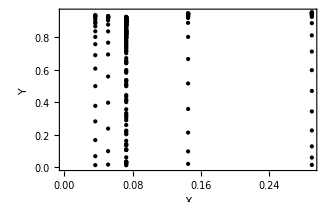

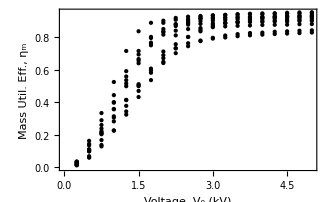

```mathematica
X=Table[ΠionT[[j]],{j,1,Nsols}];
Y=Table[ηmT[[j]],{j,1,Nsols}];
MultiCasePlot[X,Y,Automatic,Automatic,"X","Y",False]

MultiCasePlot[V0T/1000,ηmT,Automatic,Automatic,"Voltage, V_0 (kV)","Mass Util. Eff., η_m",False]
```

Thesis Plots 02-21-2022

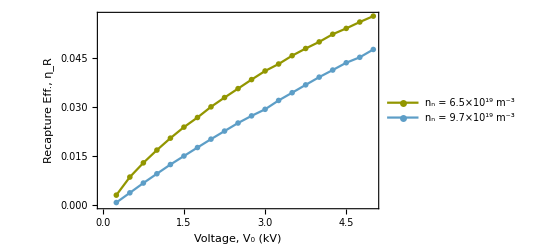

Part::partw: Part 20 of {0.18276,0.163493,0.149296,0.139264,0.132289,0.126651,0.12313,0.120231,0.117886,0.115715,0.114085,0.114207,0.113076,0.112655,0.112743,0.112514,0.112263,0.111783,0.112255} does not exist.

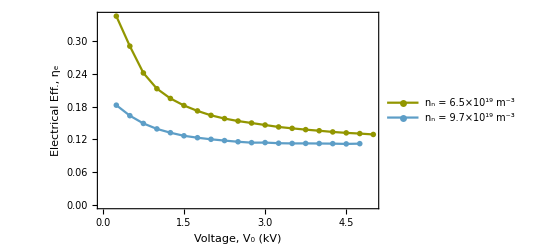

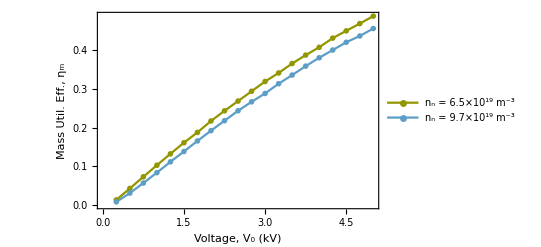

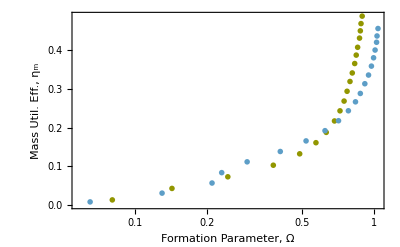

Part::partw: Part 20 of {0.18276,0.163493,0.149296,0.139264,0.132289,0.126651,0.12313,0.120231,0.117886,0.115715,0.114085,0.114207,0.113076,0.112655,0.112743,0.112514,0.112263,0.111783,0.112255} does not exist.

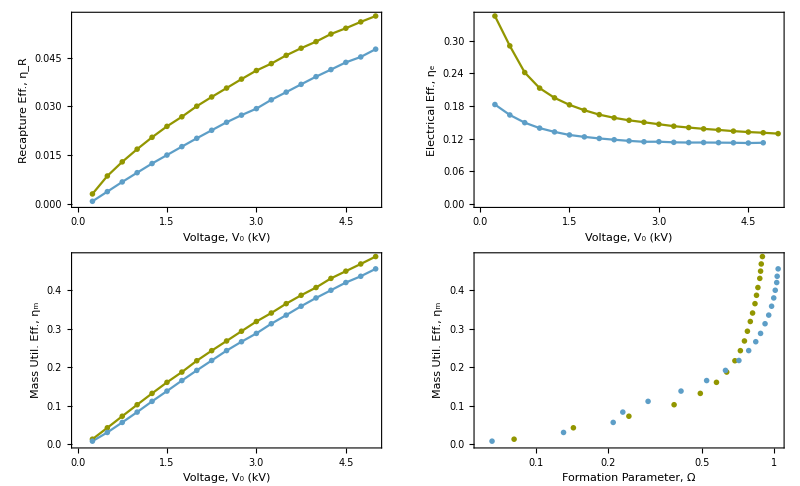

```mathematica
(** Backfill Analysis **)
V0T1 = V0T[[1;;20]];
V0T2 = V0T[[21;;40]];
EionT1 = EionT[[1;;20]];
EionT2 = EionT[[21;;40]];
ηmT1 = ηmT[[1;;20]];
ηmT2 = ηmT[[21;;40]];
ηR1 = ηTrecT[[1;;20]];
ηR2= ηTrecT[[21;;40]];
ηe1 =ηerecT[[1;;20]];
ηe2 = ηerecT[[22;;40]];

EffPlot[X1_,Y1_,X2_,Y2_,xrange_,yrange_,xlabel_,ylabel_]:=Show[{ListPlot[
{Table[{X1[[ii]],Y1[[ii]]},{ii,1,20}],
Table[{X2[[ii]],Y2[[ii]]},{ii,1,20}]},
Joined->True,PlotStyle->{ColorData[97,"ColorList"][[10]],ColorData[97,"ColorList"][[7]]},PlotRange->{xrange,yrange},PlotLegends-> {"n_n = 6.5×10^19 m^-3","n_n = 9.7×10^19 m^-3" },PlotMarkers->{●,●}]},
Frame->True,
ImageSize->400,
FrameLabel->{xlabel,ylabel},
Axes->False,
LabelStyle->{16,Black},
FrameStyle->Thickness[0.004],
FrameTicksStyle->Black,
BaseStyle->{FontFamily->"Times"}]

GridPlot[X1_,Y1_,X2_,Y2_,xrange_,yrange_,xlabel_,ylabel_]:=Show[{ListPlot[
{Table[{X1[[ii]],Y1[[ii]]},{ii,1,20}],
Table[{X2[[ii]],Y2[[ii]]},{ii,1,20}]},
Joined->True,PlotStyle->{ColorData[97,"ColorList"][[10]],ColorData[97,"ColorList"][[7]]},PlotRange->{xrange,yrange},PlotMarkers->{●,●}]},
Frame->True,
ImageSize->400,
FrameLabel->{xlabel,ylabel},
Axes->False,
LabelStyle->{16,Black},
FrameStyle->Thickness[0.004],
FrameTicksStyle->Black,
BaseStyle->{FontFamily->"Times"}]

FormPlot[X1_,Y1_,X2_,Y2_,xrange_,yrange_,xlabel_,ylabel_]:=Show[{ListLogLinearPlot[
{Table[{X1[[ii]],Y1[[ii]]},{ii,1,20}],
Table[{X2[[ii]],Y2[[ii]]},{ii,1,20}]},
Joined->False,PlotStyle->{ColorData[97,"ColorList"][[10]],ColorData[97,"ColorList"][[7]]},PlotRange->{xrange,yrange},PlotMarkers->{●,●}]},
Frame->True,
ImageSize->400,
FrameLabel->{xlabel,ylabel},
Axes->False,
LabelStyle->{16,Black},
FrameStyle->Thickness[0.004],
FrameTicksStyle->Black,
BaseStyle->{FontFamily->"Times"}]



EffPlot[V0T1/1000,ηR1,V0T2/1000,ηR2,{0,5},Automatic,"Voltage, V_0 (kV)","Recapture Eff., η_R"]
EffPlot[V0T1/1000,ηe1,V0T2/1000,ηe2,{0,5},Automatic,"Voltage, V_0 (kV)","Electrical Eff., η_e"]
EffPlot[V0T1/1000,ηmT1,V0T2/1000,ηmT2,{0,5},Automatic,"Voltage, V_0 (kV)","Mass Util. Eff., η_m"]
FormPlot[EionT1,ηmT1,EionT2,ηmT2,Automatic,Automatic,"Formation Parameter, Ω","Mass Util. Eff., η_m"]

Print[GraphicsGrid[{
{GridPlot[V0T1/1000,ηR1,V0T2/1000,ηR2,{0,5},Automatic,"Voltage, V_0 (kV)","Recapture Eff., η_R"],GridPlot[V0T1/1000,ηe1,V0T2/1000,ηe2,{0,5},Automatic,"Voltage, V_0 (kV)","Electrical Eff., η_e"]},
{GridPlot[V0T1/1000,ηmT1,V0T2/1000,ηmT2,{0,5},Automatic,"Voltage, V_0 (kV)","Mass Util. Eff., η_m"],FormPlot[EionT1,ηmT1,EionT2,ηmT2,Automatic,Automatic,"Formation Parameter, Ω","Mass Util. Eff., η_m"]}},
Spacings->{5,-5}, ImageSize-> 800]];
```